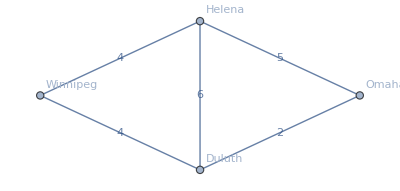

```mathematica
test = Graph[
{
"Helena"<->"Duluth",
"Helena"<->"Winnipeg",
"Winnipeg"<->"Duluth",
"Helena"<->"Omaha",
"Omaha"<->"Duluth"
},
EdgeWeight->{6,4,4,5,2},
VertexLabels->"Name",
EdgeLabels->"EdgeWeight"]
```

```mathematica
FindShortestPath[test, "Winnipeg","Omaha"]
```

{Winnipeg,Duluth,Omaha}

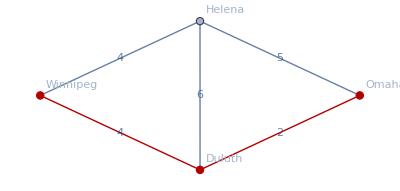

```mathematica
HighlightGraph[Graph[{"Helena", "Duluth", "Winnipeg", "Omaha"}, {UndirectedEdge["Helena", "Duluth"], UndirectedEdge["Helena", "Winnipeg"], UndirectedEdge["Winnipeg", "Duluth"], UndirectedEdge["Helena", "Omaha"], UndirectedEdge["Omaha", "Duluth"]}, {EdgeLabels -> {"EdgeWeight"}, VertexLabels -> {"Name"}, EdgeWeight -> {6, 4, 4, 5, 2}}],PathGraph[{"Winnipeg","Duluth","Omaha"}]]
```

```mathematica
FindShortestTour[test]
```

{15,{1,4,2,3,1}}

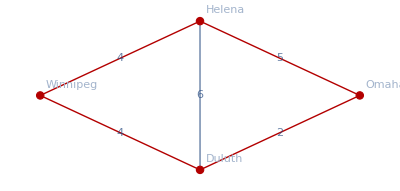

```mathematica
HighlightGraph[test,PathGraph[{"Helena", "Duluth", "Winnipeg", "Omaha"}[[%21[[2]]]]]]
```